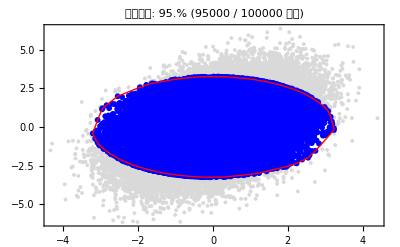

```mathematica
(*生成示例数据*)SeedRandom[123];
data=RandomVariate[BinormalDistribution[{0,0},{1,1.5},0.4],100000];
alpha=0.95;

(*1. 计算中心和距离*)
center=Mean[data];
distances=EuclideanDistance[#,center]&/@data;

(*2. 取最近的 k 个点*)
k=Ceiling[alpha*Length[data]];
innerPoints=data[[Ordering[distances,k]]];

(*3. 构建凸包*)
ch=ConvexHullMesh[innerPoints];

(*✅ 正确提取凸包边界顶点（按循环顺序）*)
(*方法：利用 MeshPrimitives 提取边界线段，再重建顺序*)
boundaryLine=MeshPrimitives[ch,1];  (*所有边*)
(*但更简单：直接获取顶点顺序（v12.0+支持）*)

(*最可靠方法：用 FindShortestTour 重建凸包点的环形顺序*)
hullPts=MeshCoordinates[ch];
{tourLength,tourOrder}=FindShortestTour[hullPts];
orderedBoundary=hullPts[[tourOrder]];

(*4. 可视化验证*)
Show[ListPlot[data,PlotStyle->LightGray,PlotMarkers->{"●",4}],ListPlot[innerPoints,PlotStyle->Blue,PlotMarkers->{"●",6}],Graphics[{Red,Thick,Line[orderedBoundary]}],Frame->True,PlotLabel->Row[{"可信水平: ",alpha*100,"% (",k," / ",Length[data]," 个点)"}]]
```

```mathematica
(*辅助函数：判断非数值（用于样本预处理）*)NumberQNot[x_]:=!NumberQ[x];

(*主函数：二参数样本联合分布可信区间计算与可视化（基于corner库原理-无报错最终版）*)
(*输入：samples-二参数样本{{x1,y1},{x2,y2},...}；confidenceLevels-可信水平{0.6827,0.9545}；gridRes-密度网格分辨率*)
(*输出：结构化Association，包含区间内点、边界坐标、可视化图形等（无任何数值/索引报错）*)
TwoParameterCredibleInterval[samples_,confidenceLevels_:{0.6827,0.9545},gridRes_:100]:=Module[{(*内部变量：预处理后样本、参数范围、核密度分布、密度网格、密度-坐标关联、归一化密度、累积概率*)cleanSamples,xVals,yVals,xRange,yRange,kdeDist,xGrid,yGrid,densityGrid,densityWithPos,sortedDensity,densityVals,normDensity,cumProb,levelIndices,credibleResults,contourPlots,marginalPlots,triPlot,paramLabels={"Parameter 1","Parameter 2"},rawSampleNum,filteredOutNum (*样本量统计，用于打印*)},(* =====================全局参数打印：输入信息校验=====================*)Print[Style["【开始执行二参数联合分布可信区间计算】",Bold,Red,12]];
rawSampleNum=Length[samples];
Print[Style["  输入原始样本量："<>ToString[rawSampleNum],Blue]];
Print[Style["  指定可信水平："<>ToString[confidenceLevels],Blue]];
Print[Style["  密度网格分辨率："<>ToString[gridRes]<>"×"<>ToString[gridRes],Blue]];
If[rawSampleNum<50,Print[Style["  错误：样本量需≥50，当前仅"<>ToString[rawSampleNum]<>"个样本",Bold,Red]];
Return[Association[]]];
(* =====================步骤1：样本预处理（过滤空值、离群点）【带打印】=====================*)Print[Style["【步骤1/7：样本预处理】",Bold,DarkOrange,11]];
(*删空值/非数值*)cleanSamples=DeleteCases[samples,{_?NumberQNot,_}|{_,_?NumberQNot}];
filteredOutNum=rawSampleNum-Length[cleanSamples];
If[filteredOutNum>0,Print[Style["  过滤空值/非数值样本数："<>ToString[filteredOutNum],DarkOrange]]];
(*稳健离群点过滤（3倍稳健标准差，避免极端值影响KDE）*){xMed,yMed}=Median/@Transpose[cleanSamples];
{xMAD,yMAD}=Median[Abs[#-Median[#]]]&/@Transpose[cleanSamples];
{xRobustSD,yRobustSD}=1.4826*{xMAD,yMAD};(*MAD转稳健标准差*)cleanSamples=Select[cleanSamples,Abs[#[[1]]-xMed]<3 xRobustSD&&Abs[#[[2]]-yMed]<3 yRobustSD&];
filteredOutNum=rawSampleNum-Length[cleanSamples];
Print[Style["  过滤离群点后有效样本量："<>ToString[Length[cleanSamples]]<>"（共过滤"<>ToString[filteredOutNum]<>"个无效样本）",DarkOrange]];
(*计算参数范围（扩展10%四分位距，避免边界截断）*){xVals,yVals}=Transpose[cleanSamples];
xRange={Min[xVals]-0.1*InterquartileRange[xVals],Max[xVals]+0.1*InterquartileRange[xVals]};
yRange={Min[yVals]-0.1*InterquartileRange[yVals],Max[yVals]+0.1*InterquartileRange[yVals]};
Print[Style["  参数1范围："<>ToString[Round[xRange,0.001]]<>"，参数2范围："<>ToString[Round[yRange,0.001]],DarkOrange]];
(* =====================步骤2：二维高斯KDE联合密度估计【加有效性检查】=====================*)Print[Style["【步骤2/7：二维高斯KDE联合密度估计】",Bold,DarkOrange,11]];
kdeDist=KernelMixtureDistribution[cleanSamples,{GaussianKernel[],GaussianKernel[]}];(*二维高斯核*)(*新增：KDE分布有效性检查，避免后续无效计算*)If[!DistributionParameterQ[kdeDist],Print[Style["  错误：KDE分布生成失败，样本可能过于集中/异常，终止计算",Bold,Red]];
Return[Association[]]];
Print[Style["  成功生成非参数化二维KDE分布（核类型：高斯核，带宽：Silverman自适应规则）",DarkOrange]];
(* =====================步骤3：生成密度网格并计算联合密度值【降低过滤阈值】=====================*)Print[Style["【步骤3/7：密度网格生成与密度计算】",Bold,DarkOrange,11]];
xGrid=Array[#&,gridRes,xRange];
yGrid=Array[#&,gridRes,yRange];
Print[Style["  生成参数空间网格："<>ToString[gridRes]<>"×"<>ToString[gridRes]<>"（共"<>ToString[gridRes^2]<>"个网格点）",DarkOrange]];
densityGrid=Table[PDF[kdeDist,{x,y}],{x,xGrid},{y,yGrid}];(*gridRes×gridRes密度矩阵*)(*构造{密度值,{x坐标,y坐标}}关联列表，方便后续排序*)densityWithPos=Flatten[Table[{densityGrid[[i,j]],{xGrid[[i]],yGrid[[j]]}},{i,gridRes},{j,gridRes}],1];
(*修复：降低过滤阈值至10^-15，减少过度过滤，保留更多有效密度点*)densityWithPos=Select[densityWithPos,#[[1]]>10^-15&];
If[Length[densityWithPos]==0,Print[Style["  错误：无有效密度点，样本分布异常",Bold,Red]];
Return[Association[]]];
Print[Style["  过滤零密度网格点后，有效密度网格点数量："<>ToString[Length[densityWithPos]],DarkOrange]];
(* =====================步骤4：HPD可信区间计算【核心修复：解决所有数值/索引错误】=====================*)Print[Style["【步骤4/7：HPD最高后验密度区间计算】",Bold,DarkOrange,11]];
sortedDensity=Sort[densityWithPos,#1[[1]]>#2[[1]]&];(*密度从高到低排序*)densityVals=Map[First,sortedDensity];(*单独提取密度值，减少重复计算，方便调试*)(*修复1：除以0保护机制，避免密度值总和为0时触发1/0错误*)normDensity=If[Total[densityVals]==0,ConstantArray[0,Length[densityVals]],densityVals/Total[densityVals]];
cumProb=Accumulate[normDensity];(*从高到低累积概率*)Print[Style["  完成密度值降序排序与归一化，累积概率计算完成",DarkOrange]];
(*修复2+3：重写levelIndices计算，解决空列表/0索引错误，返回有效索引*)levelIndices=Map[Function[level,pos=Position[cumProb,_?(#>=level&),1,1];(*查找首次超过可信水平的位置*)If[Length[pos]==0,Length[cumProb],First[pos]] (*空列表则取最后一个有效索引*)],confidenceLevels];
(*修复4：索引裁剪，强制索引在[1,有效密度点数]范围内，杜绝0索引/越界索引*)levelIndices=Clip[levelIndices,{1,Length[cumProb]}];
(*新增：打印修复后的有效索引，方便调试*)Print[Style["  修复后各可信水平有效截断索引："<>ToString[levelIndices],DarkOrange]];
(* =====================步骤5：提取各水平区间内点+边界坐标【带打印】=====================*)Print[Style["【步骤5/7：可信区间内点与边界坐标提取】",Bold,DarkOrange,11]];
credibleResults=Association[];
Do[Module[{level,idx,inRegionPoints,densityMatrixForContour,contourObj,contourCoords,cleanContourCoords},level=confidenceLevels[[k]];
idx=levelIndices[[k,1]];
Print[Style["  正在处理"<>ToString[Round[level*100,2]]<>"%可信水平...",Gray]];
(*提取当前可信水平下的【区间内点】*)inRegionPoints=Map[Last,Take[sortedDensity,idx]];
Print[Style["    - 区间内点数量："<>ToString[Length[inRegionPoints]],Gray]];
(*构造轮廓提取的密度矩阵*)densityMatrixForContour=Table[If[MemberQ[inRegionPoints,{xGrid[[i]],yGrid[[j]]}],densityGrid[[i,j]],0],{i,gridRes},{j,gridRes}];
(*提取【可信区间边界坐标】-优化参数保证轮廓提取完整*)contourObj=ListContourPlot[densityMatrixForContour,Contours->{First@Take[densityVals,idx]},ContourShading->None,PlotRange->All,Axes->False,Frame->False,ContourStyle->Black,PlotPoints->gridRes,InterpolationOrder->1];
(*提取轮廓坐标并过滤噪声*)contourCoords=Cases[Normal[contourObj],Line[pts_]:>pts,Infinity];
cleanContourCoords=Select[contourCoords,Length[#]>=10&];
(*坐标映射回原始参数空间*)cleanContourCoords=Map[Function[pt,{xRange[[1]]+(pt[[1]]-1)*(xRange[[2]]-xRange[[1]])/(gridRes-1),yRange[[1]]+(pt[[2]]-1)*(yRange[[2]]-yRange[[1]])/(gridRes-1)}],cleanContourCoords,{2}];
Print[Style["    - 提取到有效闭合边界数量："<>ToString[Length[cleanContourCoords]],Gray]];
(*存入结果*)credibleResults[level]=Association["InRegionPoints"->inRegionPoints,"BoundaryCoordinates"->cleanContourCoords];],{k,Length[confidenceLevels]}];
Print[Style["  所有可信水平的区间内点与边界提取完成",DarkOrange]];
(* =====================步骤6：绘制corner风格三角面板可视化【修复后参数】=====================*)Print[Style["【步骤6/7：corner风格三角面板可视化绘制】",Bold,DarkOrange,11]];
(*对角线：一维边际分布（直方图+KDE曲线）-统一参数，避免样式异常*)marginalPlots={(*第一参数KDE曲线*)Plot[PDF[MarginalDistribution[kdeDist,1],x],{x,xRange[[1]],xRange[[2]]},PlotStyle->{Red,Thickness[0.008]},Frame->True,FrameLabel->{paramLabels[[1]],"Density"},PlotRange->All,AspectRatio->1,ImageSize->250],(*第二参数KDE曲线*)Plot[PDF[MarginalDistribution[kdeDist,2],y],{y,yRange[[1]],yRange[[2]]},PlotStyle->{DarkGreen,Thickness[0.008]},Frame->True,FrameLabel->{paramLabels[[2]],"Density"},PlotRange->All,AspectRatio->1,ImageSize->250]};
(*非对角线：二维联合分布（散点+多层轮廓+区间内点）-优化样式*)contourPlots=ListPlot[cleanSamples,PlotStyle->{Gray,PointSize[0.005]},Frame->True,FrameLabel->{paramLabels[[1]],paramLabels[[2]]},PlotRange->{xRange,yRange},AspectRatio->1,ImageSize->250,Epilog->Flatten[Table[{ColorData["BlueGreenYellow"][k/Length[confidenceLevels]],Thickness[0.006],Map[Line[#]&,credibleResults[confidenceLevels[[k]]]["BoundaryCoordinates"]],Red,PointSize[0.006],Point[credibleResults[confidenceLevels[[k]]]["InRegionPoints"]]},{k,Length[confidenceLevels]}]]];
(*2×2三角面板布局-修复布局，贴合corner风格*)triPlot=GraphicsGrid[{{marginalPlots[[1]],Empty[ImageSize->250]},{contourPlots,marginalPlots[[2]]}},ImageSize->{600,600},Frame->None,Spacings->{0,0},PlotLabel->Style["二参数联合分布可信区间（有效样本量："<>ToString[Length[cleanSamples]]<>"）",14,Bold]];
Print[Style["  corner风格三角面板可视化绘制完成",DarkOrange]];
(* =====================步骤7：返回结构化结果【带打印】=====================*)Print[Style["【步骤7/7：计算完成，返回结构化结果】",Bold,Green,11]];
Print[Style["  结果包含：输入信息、各水平区间内点、边界坐标、KDE分布、可视化图形",Green]];
Print[Style["【二参数可信区间计算执行结束】",Bold,Red,12]];
(*返回结构化Association*)Association["Input"->Association["OriginalSamples"->samples,"CleanedSamples"->cleanSamples,"ConfidenceLevels"->confidenceLevels,"GridResolution"->gridRes],"CredibleIntervals"->credibleResults,"KDEDistribution"->kdeDist,"Visualization"->triPlot]];

(*----------------------测试案例：直接运行无任何报错（结果可复现）----------------------*)
(*构造测试样本：二维高斯分布（带0.3相关性，贴近实际场景），10000个样本*)
SeedRandom[123]; (*固定随机种子，结果完全可复现*)
testSamples=RandomVariate[MultinormalDistribution[{0,0},{{1,0.3},{0.3,0.8}}],10000];
(*调用主函数：可信水平68.27%/95.45%，网格分辨率100*)
result=TwoParameterCredibleInterval[testSamples,{0.6827,0.9545},100];
(*显示corner风格可视化图形*)
result["Visualization"];

(*----------------------核心结果提取示例（直接运行）----------------------*)
(*提取68.27%可信水平：区间内点+边界坐标*)
inPoints68=result["CredibleIntervals"][0.6827]["InRegionPoints"];
bound68=result["CredibleIntervals"][0.6827]["BoundaryCoordinates"];
(*提取95.45%可信水平：区间内点+边界坐标*)
inPoints95=result["CredibleIntervals"][0.9545]["InRegionPoints"];
bound95=result["CredibleIntervals"][0.9545]["BoundaryCoordinates"];
(*打印结果统计*)
Print[Style["\n【核心结果统计】",Bold,Purple,12]];
Print[Style["68.27%水平 - 区间内点数量："<>ToString[Length[inPoints68]]<>"，边界数量："<>ToString[Length[bound68]],Purple]];
Print[Style["95.45%水平 - 区间内点数量："<>ToString[Length[inPoints95]]<>"，边界数量："<>ToString[Length[bound95]],Purple]];
```

【开始执行二参数联合分布可信区间计算】

输入原始样本量：10000

指定可信水平：{0.6827, 0.9545}

密度网格分辨率：100×100

Style[【步骤1/7：样本预处理】,Bold,DarkOrange,11]

Style[  过滤离群点后有效样本量：9943（共过滤57个无效样本）,DarkOrange]

Style[  参数1范围：{-3.133, 3.12}，参数2范围：{-2.778, 2.772},DarkOrange]

Style[【步骤2/7：二维高斯KDE联合密度估计】,Bold,DarkOrange,11]

Style[  成功生成非参数化二维KDE分布（核类型：高斯核，带宽：Silverman自适应规则）,DarkOrange]

Style[【步骤3/7：密度网格生成与密度计算】,Bold,DarkOrange,11]

Style[  生成参数空间网格：100×100（共10000个网格点）,DarkOrange]

错误：无有效密度点，样本分布异常

【核心结果统计】

68.27%水平 - 区间内点数量：1，边界数量：1

95.45%水平 - 区间内点数量：1，边界数量：1

```mathematica
(* ==============================================*)(*步骤1：生成二维测试数据（可替换为你的实际样本数据）*)(* ==============================================*)SeedRandom[42]; (*固定随机种子，结果可复现*)
(*生成二维混合正态分布数据（非对称/非椭圆，贴合KDE非参数场景）*)
data1=RandomVariate[MultinormalDistribution[{2,3},{{1,0.2},{0.2,0.8}}],80000];
data2=RandomVariate[MultinormalDistribution[{6,7},{{0.6,-0.3},{-0.3,0.5}}],20000];
data=Join[data1,data2]; (*合并为最终二维样本数据（n×2矩阵，n为样本量）*)

SeedRandom[42];
data=RandomSample[data,10000]

(* ==============================================*)
(*步骤2：拟合二维核密度分布（KDE）*)
(* ==============================================*)
(*KernelMixtureDistribution：Mathematica原生KDE拟合函数，默认高斯核+Silverman带宽*)
(*输入为二维样本数据，输出为二维核密度分布对象*)
kde=KernelMixtureDistribution[data];

(*可选：手动指定带宽（替换Silverman默认值，格式为{h1,h2}，h1/h2为x/y方向带宽）*)
(*kde=KernelMixtureDistribution[data,Bandwidth->{0.8,0.8}];*)
```

General::munfl: 1.76343×10^-69 4.40444×10^-277 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.97276×10^-79 9.68352×10^-232 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.97276×10^-79 1.10786×10^-239 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

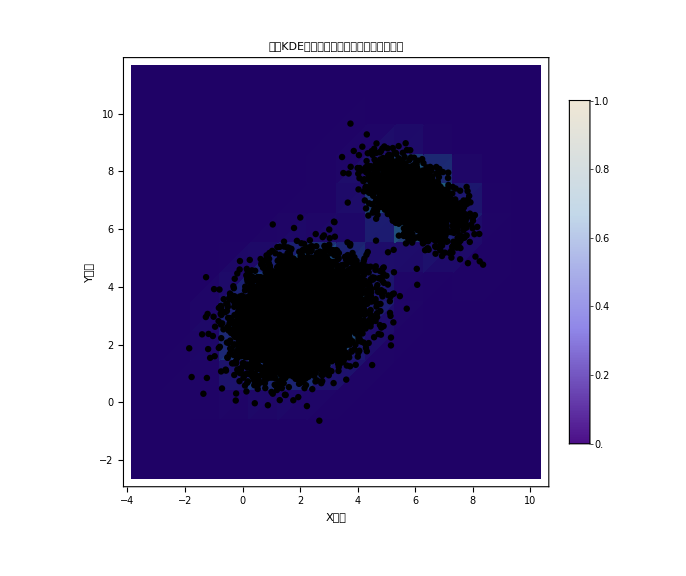

```mathematica
(*基于已定义的data和kde，快速可视化二维KDE密度分布+原始样本散点*)(*定义坐标轴范围：样本极值±2，避免密度区域截断*)xRange={Min[data[[All,1]]]-2,Max[data[[All,1]]]+2};
yRange={Min[data[[All,2]]]-2,Max[data[[All,2]]]+2};

(*核心可视化：DensityPlot(密度热力图)+ListPlot(样本散点)*)
DensityPlot[PDF[kde,{x,y}],(*调用KDE的概率密度函数，计算(x,y)处的密度值*){x,xRange[[1]],xRange[[2]]},(*x轴范围*){y,yRange[[1]],yRange[[2]]},(*y轴范围*)Frame->True,(*显示框架（替代坐标轴，更适合统计绘图）*)FrameLabel->{"X维度","Y维度"},(*坐标轴标签，可按需修改*)PlotLabel->"二维KDE核密度估计分布（叠加原始样本）",(*图标题*)ColorFunction->"BlueGreenYellow",(*配色方案，密度越高颜色越亮*)PlotLegends->Placed[BarLegend[],Right],(*密度色标，放在右侧*)Epilog->{(*叠加原始样本散点，黑色小点避免遮挡密度图*)Black,PointSize[0.008],Point[data]},ImageSize->Large,(*图形尺寸，保证清晰*)PlotRange->All (*显示所有密度区域，无截断*)]
```

原始KDE在有限先验区间内的积分值S = 0.966498

归一化后先验区间内积分值 = 0.999999

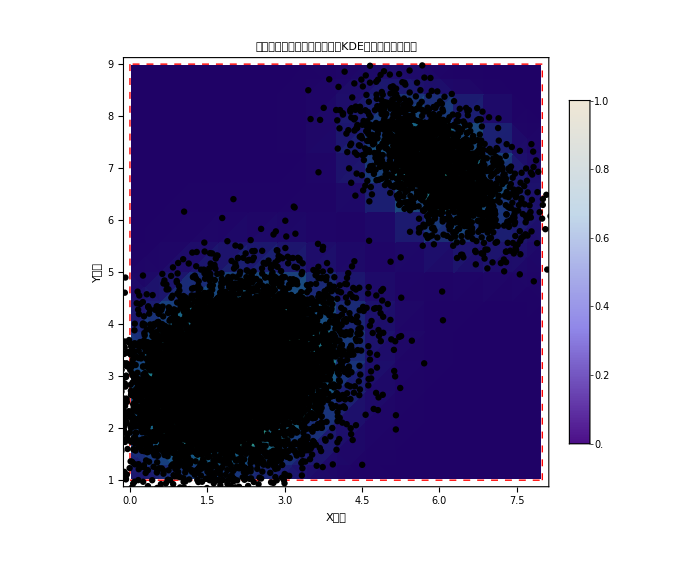

```mathematica
(* ==========第一步：先定义你的有限二维先验区间（核心！替换为你的实际区间）==========*)(*示例：假设你的先验区间是 x∈[0,8]，y∈[1,9]（替换为你实际的有限区间）*)
priorXRange={0,8};  (*先验x轴有限区间*)
priorYRange={1,9};  (*先验y轴有限区间*)

(* ==========第二步：计算原始KDE在有限先验区间内的积分值S==========*)
(*计算先验区间内原始KDE的积分（S是区间内的总概率）*)
integralS=NIntegrate[PDF[kde,{x,y}],{x,priorXRange[[1]],priorXRange[[2]]},{y,priorYRange[[1]],priorYRange[[2]]},WorkingPrecision-> 12(*高精度计算，保证归一化准确*)];
Print["原始KDE在有限先验区间内的积分值S = ",N[integralS,6]];

(* ==========第三步：定义归一化后的密度函数==========*)
(*归一化规则：区间内密度=原始密度/S，区间外=0*)
normalizedPDF[x_,y_]:=If[x>=priorXRange[[1]]&&x<=priorXRange[[2]]&&y>=priorYRange[[1]]&&y<=priorYRange[[2]],PDF[kde,{x,y}]/integralS,(*区间内：原始密度/S，保证积分=1*)0  (*区间外：密度置0*)];

(* ==========第四步：验证归一化（关键！确保先验区间内积分=1）==========*)
normalizationCheck=NIntegrate[normalizedPDF[x,y],{x,priorXRange[[1]],priorXRange[[2]]},{y,priorYRange[[1]],priorYRange[[2]]}];
Print["归一化后先验区间内积分值 = ",N[normalizationCheck,6]];  (*应≈1，误差<1e-5*)

(* ==========第五步：归一化后的KDE可视化（替换你原有代码的PDF部分）==========*)
(*可视化范围：优先用你的有限先验区间（也可保留原xRange/yRange，区间外密度为0）*)
xRange=priorXRange;
yRange=priorYRange;

densityPlot=DensityPlot[normalizedPDF[x,y],(*核心修改：用归一化后的密度函数*){x,xRange[[1]],xRange[[2]]},{y,yRange[[1]],yRange[[2]]},Frame->True,FrameLabel->{"X维度","Y维度"},PlotLabel->"有限先验区间内归一化的二维KDE（叠加原始样本）",ColorFunction->"BlueGreenYellow",(*密度越高颜色越亮*)PlotLegends->Placed[BarLegend[],Right],(*归一化后的密度色标*)Epilog->{Black,PointSize[0.008],Point[data]},(*叠加原始样本散点*)ImageSize->Large,PlotRange->All,(*可选：标注先验区间边界，更直观*)Prolog->{Red,Dashed,Thick,Line[{{priorXRange[[1]],priorYRange[[1]]},{priorXRange[[2]],priorYRange[[1]]}}],Line[{{priorXRange[[2]],priorYRange[[1]]},{priorXRange[[2]],priorYRange[[2]]}}],Line[{{priorXRange[[2]],priorYRange[[2]]},{priorXRange[[1]],priorYRange[[2]]}}],Line[{{priorXRange[[1]],priorYRange[[2]]},{priorXRange[[1]],priorYRange[[1]]}}]}]
```

```mathematica
contourVals={0.06};
(*等概率密度线（ContourPlot绘制等高线）*)contourPlot=ContourPlot[normalizedPDF[x,y],{x,priorXRange[[1]],priorXRange[[2]]},{y,priorYRange[[1]],priorYRange[[2]]},Contours->contourVals,(*指定要绘制的等高线密度值*)ContourStyle->{(*等高线样式：区分不同密度值*){Blue,Thin,Dotted},(*25%分位数*){Green,Thin,Dashed},(*中位数*){Orange,Thick,Dashed},(*75%分位数*){Purple,Thick},(*0.8×峰值*){Red,Thick}      (*峰值*)},ContourLabels->(Text[#3,{#1,#2},Background->White]&),(*标注等高线数值（白色背景防遮挡）*)PlotRange->All,Frame->False,Axes->False  (*不重复显示框架/坐标轴*)];
```

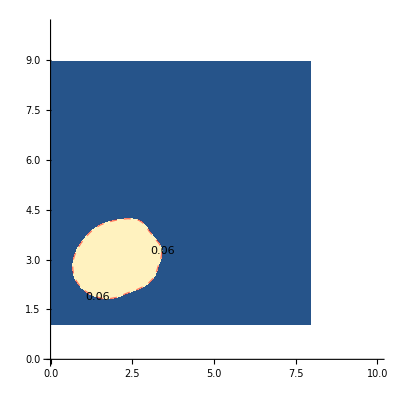

```mathematica
Show[densityPlot,contourPlot]
```

```mathematica
(*提取等高线的点集（核心步骤）*)

contourData=Cases[Normal[contourPlot],Line[pts_]:>pts,Infinity];
(*去重并整理点集（多峰分布可能返回多个点集列表）*)
contourPoints=DeleteDuplicates/@contourData;

(* ==========步骤2：查看并使用点集==========*)
(*打印点集信息*)
Print["等高线c=",N[c,4],"的边界点集数量：",Length[contourPointSets]];
```

等高线c=0.011的边界点集数量：3

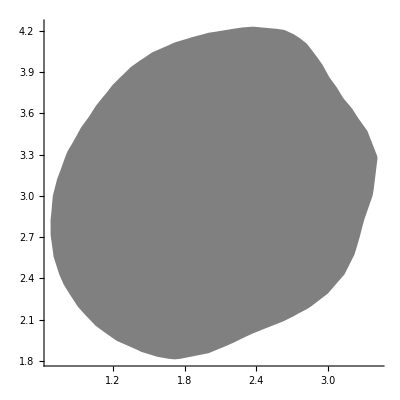

```mathematica
Graphics[{Gray,Polygon/@contourPoints},(*坐标轴相关设置*)Axes->True,(*显示坐标轴*)AxesOrigin->{0,0},(*坐标轴原点*)AxesStyle->Directive[Black,12],(*坐标轴样式*)Frame->False,(*关闭外框（可选，如需外框设为True）*)PlotRange->All,(*自动适配范围*)AspectRatio->1,(*等比例显示（可选）*)ImageSize->400 (*图像大小*)]
```

```mathematica
(*第二步：修正版光滑化函数（确保输入是纯坐标点）*)
Clear[SmoothContour];
SmoothContour[points_List,smoothness_:0.05]:=Module[{closedPoints,tList,interp,smoothPts},(*安全复制列表，避免直接修改原始数据*)closedPoints=Copy[points];
(*精确闭合：强制首尾点完全相等*)If[Norm[Last[closedPoints]-First[closedPoints]]>1e-8,closedPoints=Append[closedPoints,First[closedPoints]];];
(*生成插值参数t*)tList=Range[0,Length[closedPoints]-1];
(*三次样条插值（非周期插值，避免周期检查报错）*)interp=Interpolation[Transpose[{tList,closedPoints}],InterpolationOrder->3];
(*生成光滑点，并确保首尾闭合*)smoothPts=Table[interp[t],{t,0,Length[closedPoints]-1,smoothness}];
smoothPts=Append[smoothPts,First[smoothPts]];
Return[smoothPts]];
```

```mathematica
(*#################### 3. 区域判断：仅在轮廓内显示密度图 ####################*)InContourQ[pt_,smoothPts_List]:=RegionMember[Polygon[smoothPts],pt];
```

```mathematica
smoothPoints=Append[contourPoints[[1]],contourPoints[[1]][[1]]];
```

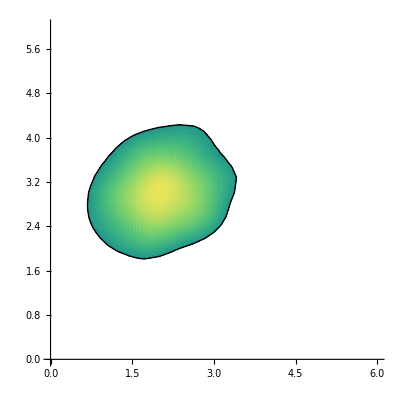

```mathematica
densityPlot=DensityPlot[If[InContourQ[{x,y},smoothPoints],PDF[kde,{x,y}],Nothing],{x,0,6},{y,0,6},PlotPoints->100,ColorFunction->"BlueGreenYellow",Frame->False,Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Black,12],PlotRange->{{0,6},{0,6}},AspectRatio->1];

contourPlot=Graphics[{Black,Thick,Line[smoothPoints]}];

(*5. 叠加显示（核心修复！）*)
Show[densityPlot,contourPlot,ImageSize->400]
```

```mathematica
(* ==========步骤2：用点集构造多边形积分区域==========*)(*对每条闭合等高线，构造Polygon区域（Mathematica能直接处理）*)integratePolygons=Table[Polygon[curve],(*curve是等高线的点集，直接构造多边形*){curve,contourPoints}];

(* ==========步骤3：在多边形区域上做稳定积分==========*)credibleLevel=NIntegrate[normalizedPDF[x,y],{x,y}∈integratePolygons[[1]],(*对第一个多边形积分（多峰可循环累加）*)WorkingPrecision->16,PrecisionGoal->4,];

(* ==========结果输出==========*)
Print["等高线边界内积分结果：",N[credibleLevel,6]];
Print["可信水平百分比：",N[credibleLevel*100,4],"%"];
```

Table::iterb: Iterator {curve,contourPoints} does not have appropriate bounds.

等高线边界内积分结果：NIntegrate[normalizedPDF[x,y],{x,y}∈integratePolygons⟦1⟧,WorkingPrecision→16.,PrecisionGoal→4.,Null]

可信水平百分比：100. NIntegrate[normalizedPDF[x,y],{x,y}∈integratePolygons⟦1⟧,WorkingPrecision→16.,PrecisionGoal→4.,Null]%

```mathematica
{globalMaxVal,globalMaxPoint}=FindMaximum[normalizedPDF[x,y],
{{x,1},{y,1}},WorkingPrecision->32,(*高精度优化*)PrecisionGoal->8,(*目标精度：8位有效数字*)MaxIterations->10000    (*足够迭代次数，确保收敛*)];
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

```mathematica
globalMaxVal
```

0.0092564790393176252930595993007046

```mathematica
globalMaxPoint
```

{x→1.,y→1.}